```mathematica
Needs["BifCurve`"]
```

```mathematica
?Funcv
```

Funcv[f, vars] returns a function suitable for use as the first argument in BifCurve, NewtRaph, or FindTangent.

```mathematica
?NewtRaph
```

NewtRaph[F, x0, varindx] refines the initial guess x0.

```mathematica
Options[NewtRaph]
```

{MaxIter→20,NRTol→1/10000000,TrapRad→1000}

```mathematica
?BifCurve
```

BifCurve[F_, x0_List, varindex_List] continues the curve defined by the function F (see Funcv).

```mathematica
Options[BifCurve]
```

{TryStep→0.01,MinStep→1.×10^-6,MaxStep→1.,NSteps→1000,IncrFactor→1.1,DecrFactor→3.,TrapFactor→2,Window→{{-∞,∞}}}

Do continuation on the equation x (1-x) + a = 0.  First, compile the function, deciding on the ordering of the variables:

```mathematica
f=Funcv[{x(1-x)+a},{x,a}];
```

Hold the first variable (x) fixed at -2.  Do Newton-Raphson on the second variable (a) to make the given function vanish.  Use initial guess a = 0.  Return the ordered pair {x,a}.

```mathematica
NewtRaph[f,{-2,0},{2}]
```

{-2,6.}

Do the same thing, but hold the second variable (a) fixed at a = 1.

```mathematica
NewtRaph[f,{0,1},{1}]
```

{-0.618034,1}

Continuation.  Take a small step in the direction of the first variable, solve for the second, repeat.

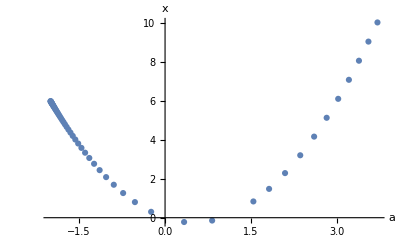

```mathematica
ListPlot[X=BifCurve[f,{-2,0},{1,2},Window->{{-5,10},{-10,10}}],AxesLabel->{"a","x"}]
```